```mathematica
XX[n_] :=If[n==0,1,- (-4)^n BernoulliB[2 n]/(2 n)!]
```

```mathematica
Table[XX[n],{n,0,10}]
```

{1,1/3,1/45,2/945,1/4725,2/93555,1382/638512875,4/18243225,3617/162820783125,87734/38979295480125,349222/1531329465290625}

```mathematica
ClearAll[YY];
YY[0,N_] := N^2/(2 Zeta[2]);
```

```mathematica
YY[n_,N_] := XX[n] N^(2n+1)/((2n +1) Zeta[2n +1]);
```

```mathematica
II[a_,b_] := Integrate[Sin[ω]^(2 a)Cos[ω]^(2 b)/(2 Pi),{ω,-Pi, Pi}, GenerateConditions->False]
(* N = 2 M , r =0,  nth moment of enstrophy*)
```

```mathematica
II[a,b]/.{(-1)^X_ :> 1}
```

(Gamma[1/2+a] Gamma[1/2+b])/(π Gamma[1+a+b])

```mathematica
ClearAll[Mom];
```

```mathematica
FullSimplify[II[0,N/2]YY[0, N]]/.(-1)^N->1
```

(6 N Gamma[(1+N)/2])/(π^(5/2) Gamma[N/2])

```mathematica
Mom[0, M_, t_] := FullSimplify[Binomial[2 M, 0]  
(II[0,M]/.{(-1)^X_ :> 1})YY[0,2 M],{n ϵ Integers, Mϵ Integers ,0 < M}]/.{ⅇ^(ⅈ M π)-> (-1)^M,Cos[X_ Pi] :> (-1)^X, (-1)^(2 M)-> 1}
```

```mathematica
Mom[0, M, t]
```

(12 M Gamma[1/2+M])/(π^(5/2) Gamma[M])

```mathematica
Mom[n_, M_, t_] :=(4 t)^(-2 n)FullSimplify[Binomial[2 M, 2 n]  
(II[n,M-n]/.{(-1)^X_ :> 1})YY[n,2 M],{n ϵ Integers, Mϵ Integers ,0 < n < M}]/.{ⅇ^(ⅈ M π)-> (-1)^M,Cos[X_ Pi] :> (-1)^X, (-1)^(2 M+n)-> (-1)^n}
```

```mathematica
Mom[0,M,1]
```

(12 M Gamma[1/2+M])/(π^(5/2) Gamma[M])

```mathematica
F[0, N_] := Mom[0,N/2, 1];
```

```mathematica
F[n_, N_] :=Mom[n,N/2, 1]/.(-1)^(n+N) -> (-1)^n
```

```mathematica
F[0, N]
```

(6 N Gamma[(1+N)/2])/(π^(5/2) Gamma[N/2])

```mathematica
ClearAll[Finf];
```

```mathematica
Finf[0] =FullSimplify[Normal[Series[F[0,N], {N, Infinity,0}]],{ N ϵ Integers,  N >0}]
```

(3 (1+8 N (-1+4 N)))/(16 √2 √N π^(5/2))

```mathematica
Finf[n_] :=FullSimplify[Normal[Series[F[n,N], {N, Infinity,0}]],{{n, N} ϵ Integers, n >0, N >0}]
```

```mathematica
Mlim= 1/2FullSimplify[μ^(3/2+ 3n)Integrate[Finf[n]E^(-μ N),{ N,0, Infinity}, GenerateConditions->False], {n ϵ Integers, n > 0}]/.μ->0
```

-((-1)^n 2^(-1/2-3 n) BernoulliB[2 n] Gamma[3/2+3 n])/(√π Gamma[1+n] Gamma[2+2 n] Zeta[1+2 n])

```mathematica
R0=1/2FullSimplify[μ^(5/2)Integrate[Finf[0]E^(-μ N),{ N,0, Infinity}, GenerateConditions->False]/.μ->0]
```

9/(4 √2 π^2)

```mathematica
Result0 = μ^(-5/2 ) R0
```

9/(4 √2 π^2 μ^(5/2))

```mathematica
Result = μ^(-3/2 - 3 n)(t + t0)^(- 2 n) Mlim
```

-((-1)^n 2^(-1/2-3 n) (t+t0)^(-2 n) μ^(-3/2-3 n) BernoulliB[2 n] Gamma[3/2+3 n])/(√π Gamma[1+n] Gamma[2+2 n] Zeta[1+2 n])

```mathematica
R1 = Result/.n->1
```

35/(1536 √2 (t+t0)^2 μ^(9/2) Zeta[3])

```mathematica
Zlim =Asymptotic[ Binomial[N,N/2]2^(-N) N^2/( 2 Zeta[2]),N->Infinity]
```

(3 √2 N^(3/2))/π^(5/2)

```mathematica
ZZ =1/2 Integrate[3 Sqrt[2]N^(3/2)/Pi^(5/2)  E^(- μ N),{N,0,Infinity}, GenerateConditions->False]
```

9/(4 √2 π^2 μ^(5/2))

```mathematica
NormResult0 = Result0/ZZ
```

1

```mathematica
NormResult = Result/ZZ
```

-((-1)^n 2^(2-3 n) π^(3/2) (t+t0)^(-2 n) μ^(1-3 n) BernoulliB[2 n] Gamma[3/2+3 n])/(9 Gamma[1+n] Gamma[2+2 n] Zeta[1+2 n])

```mathematica
NormResult/.n->1
```

(35 π^2)/(3456 (t+t0)^2 μ^2 Zeta[3])

```mathematica
BB =Table[-((-1)^n 2^(2-3 n) π^(3/2)  BernoulliB[2 n] Gamma[3/2+3 n])/(9 Gamma[1+n] Gamma[2+2 n] Zeta[1+2 n]),{n,5}]//TableForm
```

(35 π^2)/(3456 Zeta[3])
(1001 π^2)/(983040 Zeta[5])
(230945 π^2)/(528482304 Zeta[7])
(185910725 π^2)/(463856467968 Zeta[9])
(15193976525 π^2)/(24189255811072 Zeta[11])

```mathematica
N[BB,10]
```

0.08315129725
0.009692016257
0.004277271996
0.003947746107
0.006196324003

```mathematica
II[N_, q_, r_] :=(2^(-4-N) (N-q^2 r^2) Gamma[1+N])/(Gamma[1/2 (2+N-q r)] Gamma[1/2 (2+N+q r)])
```

```mathematica
II[N,q,0]
```

(2^(-4-N) N Gamma[1+N])/Gamma[(2+N)/2]^2

```mathematica
JJ =(Gamma[1/2+N/2-n] Gamma[1/2+n])/(π Gamma[1+N/2]) N(N-1)/16
```

((-1+N) N Gamma[1/2+n] Gamma[1/2-n+N/2])/(16 π Gamma[1+N/2])

```mathematica
FullSimplify[(JJ/.n->1)/II[N,q,0]]
```

1

```mathematica
"
"
```

```mathematica
576/3456
```

1/6

```mathematica
subInt[r_, l_] = {E^(X_) F_:> (F/.Solve[D[X,ω]==I r,l][[1]])}
```

{ⅇ^X_ F_:>(F/.Solve[∂_ω X==ⅈ r,l]⟦1⟧)}

```mathematica
IntR =FullSimplify[(Cos[ω]^(2M-2 n) Sin[ω]^(2 n))/.{
Cos[ω]^(2 M - 2 n) -> 2 ^(2 n-2 M) Binomial[2M-2 n,l] E^(I ω (2M-2 n-l) - I ω l),
Sin[ω]^(2 n) -> 2 ^(-2 n)(-1)^n(-1)^s Binomial[2 n,s] E^(I ω (2 n-s) - I ω s)}
 ]//Expand
```

(-1)^(n+s) 4^-M ⅇ^(-2 ⅈ (l-M+s) ω) Binomial[2 M-2 n,l] Binomial[2 n,s]

```mathematica
IntRS =IntR/.subInt[qr, l]
```

(-1)^(n+s) 4^-M Binomial[2 M-2 n,1/2 (2 M-qr-2 s)] Binomial[2 n,s]

```mathematica
SintrS=Sum[IntRS,{s,0, 2 n}]/.{qr -> q r, M ->N/2}
```

(-1)^n 2^-N Binomial[-2 n+N,1/2 (N-q r)] Hypergeometric2F1[-2 n,-N/2+(q r)/2,1-2 n+N/2+(q r)/2,-1]

```mathematica
FullSimplify[SintrS, {{n,q,r, N} ϵ Integers,0 < q r < N, n < N/2}]
```

2 (-1)^n Binomial[-2 n+N,1/2 (N-q r)] Hypergeometric2F1[1-2 n+N,1/2 (2+N+q r),1/2 (2-4 n+N+q r),-1]

```mathematica
FullSimplify[SintrS/.r->0]
```

((-1)^n Gamma[1/2 (1-2 n+N)])/(Gamma[1/2-n] Gamma[1+N/2])

```mathematica
ClearAll[BernSum];
```

```mathematica
BernSum[0,0] = 1;
BernSum[n_,m_] /; m>n:= 0;
BernSum[n_, m_] :=Sum[BernoulliB[2 j1]/(2 j1)!BernoulliB[2 j2]/(2 j2)!
BernSum[n-1, m-j1-j2] ,{j1,0,m},{j2,0,m-j1}];
```

```mathematica
S[n_,q_] :=(-1)^n Phi[1,q] - (-1)^n 2^(2 n)Sum[BernoulliB[2 j0]/(2 j0)!BernSum[n,n-j0] Phi[2 j0,q],{j0,1,n}];
```

```mathematica
ExactMom[n_, N_,q_, r_, t_] =(4 t)^(-2 n)Binomial[N, 2 n] S[n,q] SintrS
```

(-1)^n 2^(-4 n-N) t^(-2 n) Binomial[N,2 n] Binomial[-2 n+N,1/2 (N-q r)] Hypergeometric2F1[-2 n,-N/2+(q r)/2,1-2 n+N/2+(q r)/2,-1] ((-1)^n Phi[1,q]-(-1)^n 2^(2 n) TerminatedEvaluation[RecursionLimit])

```mathematica
Zeta[1]
```

ComplexInfinity

```mathematica
AS=FullSimplify[DiscreteAsymptotic[-((-1)^n 2^(2-3 n) π^(3/2)  Gamma[3/2+3 n])/(9 Gamma[1+n] Gamma[2+2 n] Zeta[1+2 n](1+2 n)!),{n,Infinity,1}]*DiscreteAsymptotic[BernoulliB[2 n], { n,Infinity,1}], {n ϵ Integers, n > 0}]/.{ⅇ^(2 ⅈ n (ⅈ+π))->E^(- 2 n),1+2^(1+2 n) ->2^(1+2 n),ⅇ^(1+2 ⅈ n π) -> E,(n/(Pi+2n Pi))^(2n)-> 1/(2Pi)^(2 n)/E,  1+2 n -> 2 n}//FullSimplify
```

(2^(-7 n) 3^(-1+3 n) π^(1-2 n))/n^2

```mathematica
(R^n  Pi/3)/n^2;
R = 3^3 Pi^(-2) 2^-7
```

27/(128 π^2)

```mathematica
ClearAll[MM];
```

```mathematica
MM[z_, L_] :=1 - Sum[(-z)^n ((-1)^n 2^(2-3 n) π^(3/2)  BernoulliB[2 n] Gamma[3/2+3 n])/(9 Gamma[1+n] Gamma[2+2 n] Zeta[1+2 n](2n)!),{n,1,L}]
```

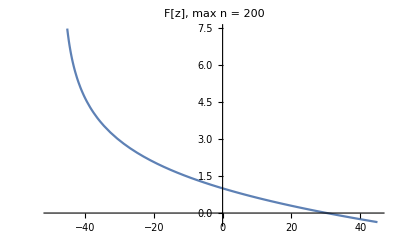

```mathematica
Plot[MM[z, 200],{z,-50,45},PlotLabel->"F[z], max n = 200"]
```

```mathematica
Table[N[MM[z,50]],{z,0,100, 0.1}]
```

```mathematica
Sum[Pi/(3n^2 )(-z/R)^n,{n,1,Infinity}]
```

1/3 π PolyLog[2,-(128 π^2 z)/27]

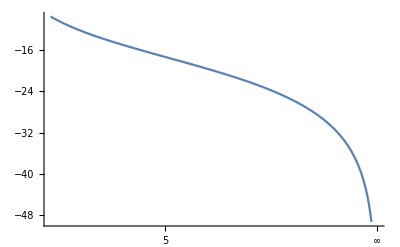

```mathematica
Plot[1/3 π PolyLog[2,-(128 π^2 z)/27],{z,1,Infinity}]
```

```mathematica
Asymptotic[Pi/3PolyLog[2,-(128 π^2 z)/27],{z , Infinity,1}]
```

-1/6 π Log[z]^2